```mathematica
a=10
```

10

```mathematica
a=a+1
```

11

```mathematica
a+=10
```

21

```mathematica
a++
```

21

```mathematica
myIncrement:=a++
```

```mathematica
?myIncrement
```

```mathematica
myIncrement
```

22

```mathematica
myIncrement
```

23

```mathematica
a
```

24

```mathematica
myIncrement
```

24

```mathematica
myIncrement
```

25

```mathematica
a
```

26

```mathematica
10==10.0
```

True

```mathematica
10===10.00
```

False

```mathematica
10.00===10.0
```

True

```mathematica
9.0===10.0
```

False

```mathematica
f[0]:=1 
f[1]:=1
f[n_]:=f[n-1]+f[n-2]
```

```mathematica
f[5]
```

8

```mathematica
DownValues[f]
```

```mathematica
{HoldPattern[f[0]]:>1,
HoldPattern[f[1]]:>1,
HoldPattern[f[n_]]:>f[n-1]+f[n-2]}
```

```mathematica
Table[f[n],{n,1,10}]
```

{1,2,3,5,8,13,21,34,55,89}

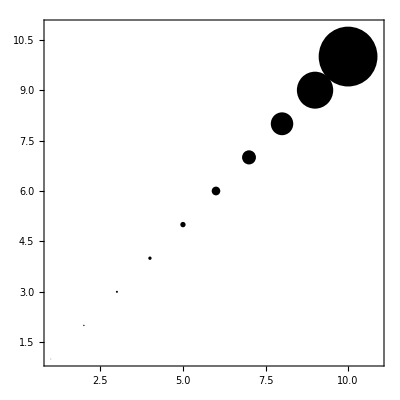

```mathematica
Show[Graphics[Table[Disk[{n,n},f[n]/100],{n,1,10}]],Frame->True]
```

```mathematica
S[n_]:=Sum[f[t],{t,1,n}]
```

```mathematica
S[1]
```

1

```mathematica
S[3]
```

6

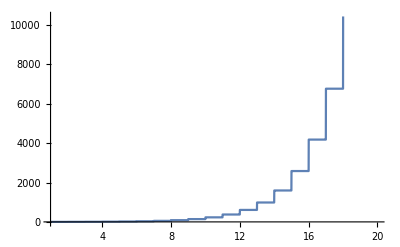

```mathematica
Plot[S[x],{x,1,20}]
```

```mathematica
S[n+1]-S[n]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of -1020+t.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of -990+t.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of -1020+t.

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

-∑_(t=1)^n Hold[f[t-1]+f[t-2]]+∑_(t=1)^(1+n) Hold[f[t-1]+f[t-2]]

```mathematica
g[0]:=10
g[1]:=20
g[n_]:=n^2
```

```mathematica
g[1]
```

20

```mathematica
g[1.2]
```

1.44

```mathematica
g[3]
```

9

关于特定值替换

```mathematica
Replace[x^2->a][x^2]
```

26

```mathematica
{x,x^2,y,z}/.x->1
```

{1,1,y,z}

```mathematica
"ab"/.("a"~~x_):>("ab"~~"b")
```

ab

```mathematica
ab/.a->ab
```

ab

```mathematica
StringReplace["ab",x___~~"a"~~y___->x~~"aba"~~y]
```

abab

```mathematica
StringReplace["abab",x___~~"a"~~y___->x~~"aba"~~y]
```

ababab

```mathematica
StringReplace[%,x___~~"a"~~y___->x~~"aba"~~y]
```

abababab

```mathematica
关于特定值替换，可以用来筛选拓扑关系。Mathematica是一个替换的艺术。
```

```mathematica
StringReplace["abcba","ba"|"bc"->"cc"]
```

acccc

```mathematica
a=StringReplace[a,"ba"|"bc"|"c"->"cbacbc"]
```

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[26,ba|bc|c→cbacbc].

StringReplace[26,ba|bc|c→cbacbc]

```mathematica
test={{{e,f},{c,d}},{{e,f},{c,d}},{{e,f},{c,d}}}//MatrixForm
```

((e
f) | (c
d)
(e
f) | (c
d)
(e
f) | (c
d))

```mathematica
Dimensions[test]
```

{1}

```mathematica
Depth[test]
```

5

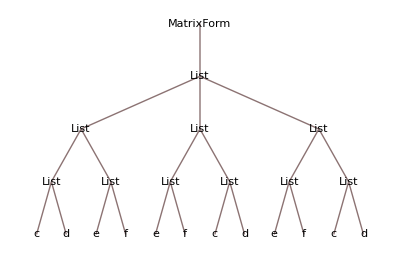

```mathematica
TreeForm[test]
```

```mathematica
Disk[
```